{p,-0.04 q+ⅇ^(-q^2/2) q}

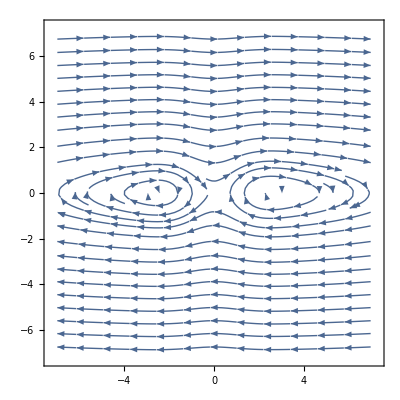

```mathematica
U=Exp[-q^2/2]+0.02 q^2;
H = 1/2 p^2+U;
vector = {D[H, p],-D[H, q]}
a=7;
StreamPlot[vector,{q,-a,a},{p,-a,a}]
(*VectorPlot[vector,{q,-a,a},{p,-a,a}]*)
```